# Running Coupling

```mathematica
ClearAll["Global`*"]
```

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

## SM parameters

```mathematica
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
aB=Exp[3.91];
aF=Exp[1.14];
```

## Running equation with an extra fermion with extra Yukawa at 500 GeV scale

### Input factors

```mathematica
κ=1/(16 π^2)(*Phase space factor*);
Nf=6;(*number of flavor why?*)
Ng=3;(*number of generation*)
z3=Zeta[3];
(*QCD*)
CA=3;(*Casimir operator Subscript[C, A]=Subscript[C, 2](adj)*)
CF=4/3;(*Casimir operator Subscript[C, F]=Subscript[C, 2](fund)*)
TR=1/2;(*Index Subscript[T, R](fund)*)
dR=3;(*dimension of representation, can be understood as color factor*)
SmoothUnitStep[x_]:=ArcTan[10x]/π+1/2;
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;
g3mZ=√(4π*αsmZ);
αsmZ=0.1179;

(*Measured pole masses*)
mhpole=125.10;
mtpole=172.76;

(*MSbar couplings*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);
ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);
g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;
```

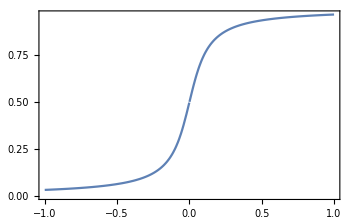

```mathematica
Plot[SmoothUnitStep[x],{x,-1,1}]
```

### Beta functions

Model: Extra vectorlike leptons Lbar, E, L, Ebar. After the first ssb, it becomes charged Dirac fermions. Let’s name them E and Ebar. These both have SM hypercharge Y=±1.

```mathematica
βyt[λ_,yt_,g3_,g2_,g1_,yN_]:=2yt(κ yt^2(3/4+1/2 dR)+κ g3^2(-3CF)+3 κ^2 λ^2+(-6)κ^2 yt^2 λ+κ^2 yt^4(3/4-9/4 dR)+κ^2 g3^2 yt^2(6CF+5/2 CF dR)+κ^2 g3^4(-3/2 CF^2-97/6 CA CF+10/3 Nf TR CF)+κ^3 λ^3(-18)+κ^3 yt^2 λ^2(285/8-45/4 dR)+κ^3 yt^4 λ(63/2+45/2 dR)+κ^3 yt^6(-345/32+107/32 dR+39/16 dR^2+9/4 z3+3/2 z3 dR)+κ^3 g3^2 yt^2 λ(6CF)+κ^3 g3^2 yt^4(-57/2 CF-81/8 CF dR)+κ^3 g3^4 yt^2(471/16 CF^2-119/8 CF^2 dR+25TR CF+717/16 CA CF+77/4 CA CF dR-33/4 Nf TR CF-4Nf TR CF dR-27z3 CF^2+18z3 CF^2 dR-27/2 z3 CA CF-9 z3 CA CF dR)+κ^3 g3^6(-129/2 CF^3+129/4 CA CF^2-11413/108 CA^2 CF+46Nf TR CF^2+556/27 Nf CA TR CF+140/27 Nf^2 TR^2 CF-48z3 Nf TR CF^2+48z3 Nf CA TR CF))+
yt κ(-9/4 g2^2-17/12 g1^2)+
yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45 Ng)+58/57 g1^4*2-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-Ng)g2^4+9 g2^2 g3^2);
βg3[λ_,yt_,g3_,g2_,g1_,yN_]:=2g3(κ g3^2(-11/6 CA+2/3 Nf TR)+κ^2 g3^2 yt^2(-2TR)+κ^2 g3^4(-17/3 CA^2+2Nf TR CF+10/3 Nf CA TR)+κ^3 g3^2 yt^4(9/2 TR+7/2 TR dR)+κ^3 g3^4 yt^2(-3TR CF-12CA TR)+κ^3 g3^6(-2857/108 CA^3-Nf TR CF^2+205/18 Nf CA TR CF+1415/54 Nf CA^2 TR-22/9 Nf^2 TR^2 CF-79/27 Nf^2 CA TR^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_,yN_]:=-g1^3 κ(-1/6-20/9 Ng+2/3*2)+g1^3 κ^2 5/3(199/30 g1^2+6/5*2 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_,yN_]:=-g2^3 κ(43/6-4/3 Ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);
βλ[λ_,yt_,g3_,g2_,g1_,t_,yN_]:=2(12κ λ^2+2κ yt^2 λ dR+κ yt^4(-dR)+κ (yN SmoothUnitStep[t-Log[500/mZ]])^4(-2)+κ^2 λ^3(-156)+κ^2 yt^2 λ^2(-24dR)+κ^2 yt^4 λ(-1/2 dR)+κ^2 yt^6(5dR)+κ^2 g3^2 yt^2 λ(10CF dR)+κ^2 g3^2 yt^4(-4CF dR)+κ^3 λ^4(3588+2016z3)+κ^3 yt^2 λ^3(291dR)+κ^3 yt^4 λ^2(789/2 dR-36 dR^2+252z3 dR)+κ^3 yt^6 λ(-1881/8 dR+80 dR^2-66z3 dR)+κ^3 yt^8(13/2 dR-195/8 dR^2-12z3 dR)+κ^3 g3^2 yt^2 λ^2(-306CF dR+288z3 CF dR)+κ^3 g3^2 yt^4 λ(895/4 CF dR-324 z3 CF dR)+κ^3 g3^2 yt^6(-19/2 CF dR+60z3 CF dR)+κ^3 g3^2 yt^2 λ(-119/2 CF^2 dR+77CA CF dR-16Nf TR CF dR+72z3 CF^2 dR-36z3 CA CF dR)+κ^3 g3^4 yt^4(131/2 CF^2 dR+48TR CF dR-109/2 CA CF dR+10Nf TR CF dR-48z3 CF^2 dR+24z3 CA CF dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10Ng)g2^4-39/4 g2^2 g1^2-(687/200+2Ng)25/9 g1^4+60/19*2 g1^4)2λ+(497/8-8Ng)g2^6-(97/40+8/5 Ng)5/3 g2^4 g1^2-(717/200+8/5 Ng)25/9 g2^2 g1^4-(531/1000+24/25 Ng)125/27 g1^6-1728/505*2 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10 *2 λ yt^2(17/12 g1^2+9/4 g2^2));
```

```mathematica
25/9*29/45
```

145/81

```mathematica
(1/6)^2*2+(2/3)^2+(1/3)^2
```

11/18

```mathematica
3*(2*(1/6)^2+(2/3)^2+(1/3)^2)+2(1/2)^2+1
```

10/3

```mathematica
3*(2*(1/6)^4+(2/3)^4+(1/3)^4)+2(1/2)^4+1
```

95/54

```mathematica
3*(2*(1/6)^6+(2/3)^6+(1/3)^6)+2(1/2)^6+1
```

2525/1944

```mathematica
24/25*125/27/(2525/1944)
```

1728/505

```mathematica
50/9/(95/54)
```

60/19

```mathematica
3*(1/6)^2+(1/2)^2
```

1/3

```mathematica
145/81/(95/54)
```

58/57

```mathematica
19/15*25/9(*Fermion contribution to g1^5 from 2-loop paper*)
```

95/27

```mathematica
3*95/27+1/2(*total contribution to g1^5 from the 2-loop paper*)
```

199/18

```mathematica
5/3*199/30(*total contribution to g1^5 from the code above*)
```

199/18

## Benchmark I: v_R=10^5 GeV

Here discuss the physics if v_R=10^5 GeV.

## Upper and lower limit for the extra Yukawa

```mathematica
vR=10^5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.6,0.8,0.05}]
```

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

{{0.6,0.0312864,0.401949,-2150.57},{0.65,0.0248053,0.498694,-6661.99},{0.7,0.0166726,0.677059,4075.62},{0.75,0.00664304,1.00188,1363.16},{0.8,-0.00553822,0.837927+0. ⅈ,753.389}}

So y_N=0.8 here already makes the λ runs negative. However the tunneling action at 10vR is still large and safe. So we do not need to worry about the metastability here. Now let’s first find the critical value of the Yukawa that makes λ to runs negative at v_R=10^5 GeV.

```mathematica
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
```

0.778418

So the y_N should be smaller than this value. Now let’s find the minimal Yukawa for the sake of the SFOPT.

```mathematica
PTstrengthlist={#1,#3}&@@@ Drop[list,{-1}];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN]
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.7}]
```

InterpolatingFunction::dmval: Input value {0.76706} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.751138} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.749776

So the minimal value of y_N is here. This is a quite stringent bound. The Yukawa should be within the range of 0.749 to 0.778, a small range.

## Escape point for pseudo-bounce, and metastability

We first check the pseudo-bounce solution for the smallest allowed Yukawa coupling.

-Graphics-

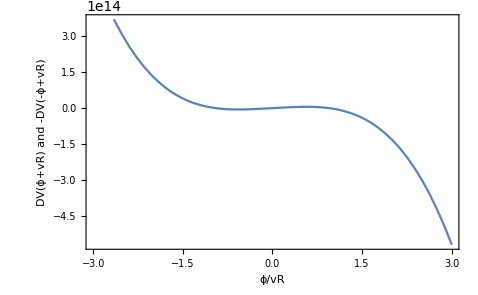

```mathematica
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
Plot[Vb[r*vR],{r,-3,3},FrameLabel->{"ϕ/vR","V(ϕ+vR) and V(-ϕ+vR)"}]
Plot[DVb[r*vR],{r,-3,3},FrameLabel->{"ϕ/vR","DV(ϕ+vR) and -DV(-ϕ+vR)"}]
```

```mathematica
ϕi=10vR;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
rf=1/ϕi*10^2;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
sol=NDSolve[{ϕ''[r]+3/r ϕ'[r]==DVb[ϕ[r]],ϕ[ri]==ϕi,ϕ'[ri]==0,WhenEvent[{ϕ[r]<0},{flago=1;"StopIntegration"}]},ϕ,{r,ri,rf}];
ϕsol[r_]:=(ϕ[r]/.sol)[[1]];
If[flago==1,riover=ri,riuder=ri];
]
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}]
```

1154.94

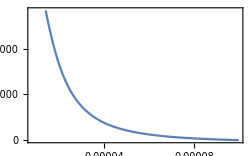

```mathematica
Plot[ϕsol[r],{r,ri,rf}]
```

```mathematica
tab={};
For[i=1,i<20,i++,
ϕi=i*10vR;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
rf=1/ϕi*10^3;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
sol=NDSolve[{ϕ''[r]+3/r ϕ'[r]==DVb[ϕ[r]],ϕ[ri]==ϕi,ϕ'[ri]==0,WhenEvent[{ϕ[r]<0},{flago=1;"StopIntegration"}]},ϕ,{r,ri,rf}];
ϕsol[r_]:=(ϕ[r]/.sol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

MapThread::mptd: Object InterpolatingFunction[{{3.11087×10^-6,0.000499987}},{5.,7.,2.,{264.},{4.},0.,0.,0.,0.,Automatic,«3»},{{3.11087×10^-6,3.11087×10^-6,3.11087×10^-6,3.11087×10^-6,«23»,«23»,«23»,3.11087×10^-6,3.11087×10^-6,3.11087×10^-6,«254»}},«1»,{Automatic}][«1»] at position {2, 2} in MapThread[NIntegrate`InterpolatingFunctionDump`invg[r,#1,#2]&,{{r},InterpolatingFunction[{{3.11087×10^-6,0.000499987}},{5.,7.,2.,{264.},{4.},0.,0.,0.,0.,Automatic,«3»},{{«1»}},{Developer`PackedArrayForm,{«1»},{2.×10^6,0.,-3.27453×10^17,«5»,-3.27453×10^17,2.×10^6,«782»}},{Automatic}][«1»]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object «1» at position {2, 2} in MapThread[NIntegrate`InterpolatingFunctionDump`invg[r,#1,#2]&,{{r},«1»}] has only 0 of required 1 dimensions.

NDSolve::ndsz: At r == 2.94147×10^-7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 4.41191×10^-7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 5.14713×10^-7, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{{1000000,1119.95,254.247},{2000000,843.286,150.709},{3000000,734.431,121.453},{4000000,670.565,106.375},{5000000,626.872,96.673},{6000000,594.382,89.6945},{7000000,568.912,84.3328},{8000000,548.198,80.0298},{9000000,530.893,76.4684},{10000000,516.131,73.452},{11000000,503.331,70.851},{12000000,492.082,68.5759},{13000000,482.086,66.5623},{14000000,473.12,64.7626},{15000000,465.014,63.1407},{16000000,457.634,61.6686},{17000000,-1.42553×10^29,-1.42553×10^29},{18000000,-1.50502×10^29,-1.50502×10^29},{19000000,-1.58356×10^29,-1.58356×10^29}}

I cannot go further due to numerical issue. But here it shows that the action seems to converge to a value around 450. But for the following let’s play an exponential trick.

```mathematica
dVexp[y_]:=DVb[ⅇ^y];
```

```mathematica
tab={};
For[i=1,i<30,i++,
ϕi=i*10vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
```

```mathematica
tab
```

{{1000000,1119.95,254.247},{2000000,843.286,150.709},{3000000,734.431,121.452},{4000000,670.565,106.375},{5000000,626.872,96.6724},{6000000,594.382,89.6941},{7000000,568.911,84.3323},{8000000,548.198,80.0294},{9000000,530.892,76.468},{10000000,516.131,73.4517},{11000000,503.33,70.8507},{12000000,492.081,68.5756},{13000000,482.085,66.5621},{14000000,473.12,64.7624},{15000000,465.013,63.1405},{16000000,457.634,61.6683},{17000000,450.875,60.3237},{18000000,444.652,59.0889},{19000000,438.895,57.9494},{20000000,433.547,56.8933},{21000000,428.56,55.9108},{22000000,423.894,54.9934},{23000000,419.514,54.1343},{24000000,415.392,53.3272},{25000000,411.502,52.5672},{26000000,407.823,51.8497},{27000000,404.335,51.1707},{28000000,401.021,50.527},{29000000,397.868,49.9155}}

OK numerical issue is not here.

```mathematica
tab={};
For[i=2,i<8,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -15.8778 and x = -15.8778.

{{1.×10^6,1119.95,254.247},{3.16228×10^6,722.021,118.423},{1.×10^7,516.131,73.4517},{3.16228×10^7,390.267,48.446},{1.×10^8,309.233,33.3121},{3.16228×10^8,254.478,23.9114}}

Now we can solve the location where new physics is required.

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
```

1.5124×10^-42

```mathematica
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{431.231}

This is the number we need, the lower bound for the SE.

```mathematica
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ]
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,8}]
```

7.30862

Notice that this is the distance above from the v_R. So we should add v_R to get the correct location. But that’s a very small correction.

```mathematica
escapefinal=10^escape+vR
escapefinal/vR
```

2.04525×10^7

204.525

So new physics is required around 200 v_R.

## 500GeV scale extra fermion

```mathematica
list500GeV={};
```

## v_R=10^5 GeV

```mathematica
vR=10^5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.6,0.85,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.8}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.75}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::nrnum: The function value 1.56658×10^9 ((-1.44072×10^8+0. ⅈ)+((-1.2003+0. ⅈ)+Null)^2)-8.35216×10^12 ((-1.2003+0. ⅈ)+Null)-(((-1.2003+0. ⅈ)+Null) (4.63599×10^-32+2 («1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((-1.2003+0. ⅈ)+Null) (4.63599×10^13+2 (2.92982×10^13-Plus[«2»]^(3/2))-0.353553 «1»-Abs[6.45255×10^8+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^19 (-0.00490651-(3 (1.80642×10^18 Log[Times[«2»]]+1.66542×10^18 Log[Times[«2»]]-2.57528×10^19 Log[Times[«2»]]-2.73067×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

FindMinimum::nrnum: The function value 1.56658×10^9 ((-1.44072×10^8+0. ⅈ)+((-1.08027+0. ⅈ)+Null)^2)-8.35216×10^12 ((-1.08027+0. ⅈ)+Null)-(((-1.08027+0. ⅈ)+Null) (4.63599×10^-32+2 («24»-«1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((-1.08027+0. ⅈ)+Null) (4.63599×10^13+2 (2.92982×10^13-Plus[«2»]^(3/2))-0.353553 «1»-Abs[6.45255×10^8+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^19 (-0.00490651-(3 (1.80642×10^18 Log[Times[«2»]]+1.66542×10^18 Log[Times[«2»]]-2.57528×10^19 Log[Times[«2»]]-2.73067×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

FindMinimum::nrnum: The function value 1.56658×10^9 ((-1.44072×10^8+0. ⅈ)+((-0.960241+0. ⅈ)+Null)^2)-8.35216×10^12 ((-0.960241+0. ⅈ)+Null)-(((-0.960241+0. ⅈ)+Null) (4.63599×10^-32+2 («24»-«1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((-0.960241+0. ⅈ)+Null) (4.63599×10^13+2 (2.92982×10^13-Plus[«2»]^(3/2))-0.353553 «1»-Abs[6.45255×10^8+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^19 (-0.00490651-(3 (1.80642×10^18 Log[Times[«2»]]+1.66542×10^18 Log[Times[«2»]]-2.57528×10^19 Log[Times[«2»]]-2.73067×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,100000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.780972

0.752654

```mathematica
tab={};
For[i=2,i<8,i++,
ϕi=0.5*10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -15.5896 and x = -15.5896.

{{500000.,2.61861×10^7,2.61849×10^7},{1.58114×10^6,913.97,173.288},{5.×10^6,623.123,95.9775},{1.58114×10^7,456.399,61.5483},{5.×10^7,352.004,41.2798},{1.58114×10^8,283.489,28.882}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,7}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list500GeV,{5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{431.231}

7.29959

2.00339×10^7

200.339

## v_R=10^5.5 GeV

```mathematica
vR=10^5.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.5,0.74,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.7}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::nrnum: The function value 4.91164×10^19+5.38936×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

FindMinimum::nrnum: The function value 4.48169×10^19+5.34888×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

FindMinimum::nrnum: The function value 4.07499×10^19+5.30862×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,316228.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.707024

0.66251

```mathematica
tab={};
For[i=2,i<8,i++,
ϕi=0.5*10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

{{1.58114×10^6,3.09452×10^8,3.09448×10^8},{5.×10^6,2.98192×10^6,2.98061×10^6},{1.58114×10^7,1029.58,191.646},{5.×10^7,706.283,105.629},{1.58114×10^8,528.168,66.5036},{5.×10^8,417.798,45.0021}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,8}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list500GeV,{5.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{435.836}

8.61042

4.08093×10^8

1290.5

## v_R=10^6 GeV

```mathematica
vR=10^6;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.5,0.74,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.6}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.71923×10^21+3.83166×10^21 ⅈ is not a real number at {ϕ} = {1.×10^6}.

FindMinimum::nrnum: The function value 1.21914×10^21+3.76535×10^21 ⅈ is not a real number at {ϕ} = {1.×10^6}.

FindMinimum::nrnum: The function value 7.21816×10^20+3.70023×10^21 ⅈ is not a real number at {ϕ} = {1.×10^6}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,1000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.645135

0.589775

```mathematica
tab={};
For[i=2,i<10,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.5528 and x = -20.5528.

{{1.×10^7,9.70228×10^7,9.70193×10^7},{3.16228×10^7,938109.,936552.},{1.×10^8,1223.06,223.071},{3.16228×10^8,849.072,123.516},{1.×10^9,643.093,78.0217},{3.16228×10^9,514.631,53.2836},{1.×10^10,427.88,38.5046},{3.16228×10^10,365.764,29.0609}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,10}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list500GeV,{6,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{440.442}

9.91486

8.22076×10^9

8220.76

## v_R=10^6.5 GeV

```mathematica
vR=10^6.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.4,0.7,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.6}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::nrnum: The function value 1.85169×10^23+2.97326×10^23 ⅈ is not a real number at {ϕ} = {3.16228×10^6}.

FindMinimum::nrnum: The function value 1.49812×10^23+2.91851×10^23 ⅈ is not a real number at {ϕ} = {3.16228×10^6}.

FindMinimum::nrnum: The function value -2.48687×10^17 ((0.-23294. ⅈ)+Null)+1.22017×10^12 ((5.42611×10^10+0. ⅈ)+((0.-23294. ⅈ)+Null)^2)-(((0.-23294. ⅈ)+Null) (4.44885×10^-32+2 («1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((0.-23294. ⅈ)+Null) (1.40685×10^18+2 (8.5912×10^17-Plus[«2»]^(3/2))-«19» («1»)^(«1»)-Abs[6.27772×10^11+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^25 (-0.00583519-1.89977×10^-28 (1.63344×10^24 Log[Times[«2»]]+1.57639×10^24 Log[Times[«2»]]-9.85089×10^24 Log[Times[«2»]]-1.71041×10^25 Log[Times[«2»]])) is not a real number at {ϕ} = {3.16228×10^6}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,3.16228×10^6} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.591246

InterpolatingFunction::dmval: Input value {0.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.525378

```mathematica
tab={};
For[i=4,i<12,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -21.2212 and x = -21.2212.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.7214 and x = -20.7214.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.2109 and x = -20.2109.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

{{3.16228×10^8,1847.94,384.949},{1.×10^9,1209.52,191.786},{3.16228×10^9,890.273,115.152},{1.×10^10,700.545,76.3823},{3.16228×10^10,576.035,54.1589},{1.×10^11,488.561,40.3305},{3.16228×10^11,423.932,31.181},{1.×10^12,374.305,24.8272}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,11}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list500GeV,{6.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{445.047}

11.3201

2.08987×10^11

66087.6

## v_R=10^7 GeV

```mathematica
vR=10^7;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.4,0.6,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.5}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.5}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
vR=10^4;
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.34284×10^24+2.04996×10^25 ⅈ is not a real number at {ϕ} = {1.×10^7}.

FindMinimum::nrnum: The function value -3.72547×10^24+1.97177×10^25 ⅈ is not a real number at {ϕ} = {1.×10^7}.

FindMinimum::nrnum: The function value -7.71561×10^18 ((0.-117602. ⅈ)+Null)+1.14482×10^13 ((1.38303×10^12+0. ⅈ)+((0.-117602. ⅈ)+Null)^2)-(((0.-117602. ⅈ)+Null) (4.39311×10^-32+2 («24»-«1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((0.-117602. ⅈ)+Null) (4.39311×10^19+2 (2.65131×10^19-Plus[«2»]^(3/2))-«19» («1»)^(«1»)-Abs[6.22517×10^12+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^27 (-0.00688353-(3 (1.58116×10^26 Log[Times[«2»]]+1.55011×10^26 Log[Times[«2»]]-7.54433×10^26 Log[Times[«2»]]-1.51519×10^27 Log[Times[«2»]]))/(160000000000000000000000000000 π^2)) is not a real number at {ϕ} = {1.×10^7}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,10000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.542775

0.46425

```mathematica
tab={};
For[i=6,i<14,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab(*Here the escape point unit should be TeV!*)
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.4559 and x = -20.4559.

{{1.×10^7,1230.4,171.415},{3.16228×10^7,947.795,109.665},{1.×10^8,768.794,75.9845},{3.16228×10^8,645.907,55.6809},{1.×10^9,556.581,42.5399},{3.16228×10^9,488.819,33.562},{1.×10^10,435.693,27.1608},{3.16228×10^10,392.941,22.4369}}

```mathematica
vR=10^7;(*Back to GeV*)
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,10}]
escapefinal=10^(escape+3)+vR
escapefinal/vR
AppendTo[list500GeV,{7,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{449.652}

9.85689

7.19272×10^12

719272.

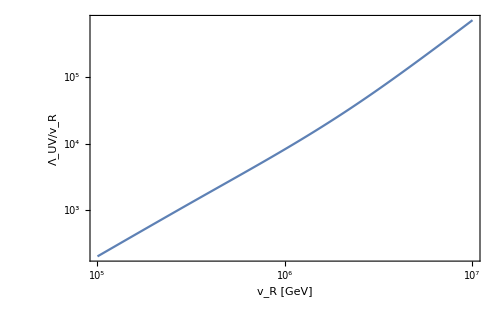

```mathematica
plot500GeV=ListLinePlot[{#1,Log10[#2]}&@@@list500GeV,InterpolationOrder->3,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["v_R [GeV]",FontFamily->"Times",FontSize->22],Style["Λ_UV/v_R",FontFamily->"Times",FontSize->22]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->22],PlotRangePadding->None,ImageSize->500,FrameTicks->{{myTicks[2,7,1],None},{myTicks[3,8,1],None}},PlotRange->{{5,7},Automatic}]
```

## 1TeV scale Extra Fermion

```mathematica
βyt[λ_,yt_,g3_,g2_,g1_,yN_]:=2yt(κ yt^2(3/4+1/2 dR)+κ g3^2(-3CF)+3 κ^2 λ^2+(-6)κ^2 yt^2 λ+κ^2 yt^4(3/4-9/4 dR)+κ^2 g3^2 yt^2(6CF+5/2 CF dR)+κ^2 g3^4(-3/2 CF^2-97/6 CA CF+10/3 Nf TR CF)+κ^3 λ^3(-18)+κ^3 yt^2 λ^2(285/8-45/4 dR)+κ^3 yt^4 λ(63/2+45/2 dR)+κ^3 yt^6(-345/32+107/32 dR+39/16 dR^2+9/4 z3+3/2 z3 dR)+κ^3 g3^2 yt^2 λ(6CF)+κ^3 g3^2 yt^4(-57/2 CF-81/8 CF dR)+κ^3 g3^4 yt^2(471/16 CF^2-119/8 CF^2 dR+25TR CF+717/16 CA CF+77/4 CA CF dR-33/4 Nf TR CF-4Nf TR CF dR-27z3 CF^2+18z3 CF^2 dR-27/2 z3 CA CF-9 z3 CA CF dR)+κ^3 g3^6(-129/2 CF^3+129/4 CA CF^2-11413/108 CA^2 CF+46Nf TR CF^2+556/27 Nf CA TR CF+140/27 Nf^2 TR^2 CF-48z3 Nf TR CF^2+48z3 Nf CA TR CF))+
yt κ(-9/4 g2^2-17/12 g1^2)+
yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45 Ng)+58/57 g1^4*2-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-Ng)g2^4+9 g2^2 g3^2);
βg3[λ_,yt_,g3_,g2_,g1_,yN_]:=2g3(κ g3^2(-11/6 CA+2/3 Nf TR)+κ^2 g3^2 yt^2(-2TR)+κ^2 g3^4(-17/3 CA^2+2Nf TR CF+10/3 Nf CA TR)+κ^3 g3^2 yt^4(9/2 TR+7/2 TR dR)+κ^3 g3^4 yt^2(-3TR CF-12CA TR)+κ^3 g3^6(-2857/108 CA^3-Nf TR CF^2+205/18 Nf CA TR CF+1415/54 Nf CA^2 TR-22/9 Nf^2 TR^2 CF-79/27 Nf^2 CA TR^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_,yN_]:=-g1^3 κ(-1/6-20/9 Ng+2/3*2)+g1^3 κ^2 5/3(199/30 g1^2+6/5*2 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_,yN_]:=-g2^3 κ(43/6-4/3 Ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);
βλ[λ_,yt_,g3_,g2_,g1_,t_,yN_]:=2(12κ λ^2+2κ yt^2 λ dR+κ yt^4(-dR)+κ (yN SmoothUnitStep[t-Log[1000/mZ]])^4(-2)+κ^2 λ^3(-156)+κ^2 yt^2 λ^2(-24dR)+κ^2 yt^4 λ(-1/2 dR)+κ^2 yt^6(5dR)+κ^2 g3^2 yt^2 λ(10CF dR)+κ^2 g3^2 yt^4(-4CF dR)+κ^3 λ^4(3588+2016z3)+κ^3 yt^2 λ^3(291dR)+κ^3 yt^4 λ^2(789/2 dR-36 dR^2+252z3 dR)+κ^3 yt^6 λ(-1881/8 dR+80 dR^2-66z3 dR)+κ^3 yt^8(13/2 dR-195/8 dR^2-12z3 dR)+κ^3 g3^2 yt^2 λ^2(-306CF dR+288z3 CF dR)+κ^3 g3^2 yt^4 λ(895/4 CF dR-324 z3 CF dR)+κ^3 g3^2 yt^6(-19/2 CF dR+60z3 CF dR)+κ^3 g3^2 yt^2 λ(-119/2 CF^2 dR+77CA CF dR-16Nf TR CF dR+72z3 CF^2 dR-36z3 CA CF dR)+κ^3 g3^4 yt^4(131/2 CF^2 dR+48TR CF dR-109/2 CA CF dR+10Nf TR CF dR-48z3 CF^2 dR+24z3 CA CF dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10Ng)g2^4-39/4 g2^2 g1^2-(687/200+2Ng)25/9 g1^4+60/19*2 g1^4)2λ+(497/8-8Ng)g2^6-(97/40+8/5 Ng)5/3 g2^4 g1^2-(717/200+8/5 Ng)25/9 g2^2 g1^4-(531/1000+24/25 Ng)125/27 g1^6-1728/505*2 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10 *2 λ yt^2(17/12 g1^2+9/4 g2^2));
```

```mathematica
list1TeV={};
```

## v_R=10^5 GeV

```mathematica
vR=10^5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.6,0.85,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.8}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.8}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.62124×10^9 ((-1.28421×10^8+0. ⅈ)+((-11.3323+0. ⅈ)+Null)^2)-8.35216×10^12 ((-11.3323+0. ⅈ)+Null)-(((-11.3323+0. ⅈ)+Null) (4.63599×10^-32+2 («23»-«1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((-11.3323+0. ⅈ)+Null) (4.63599×10^13+2 (2.92982×10^13-Plus[«2»]^(3/2))-0.353553 «1»-Abs[6.45255×10^8+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^19 (-0.00637439-(3 (1.80642×10^18 Log[Times[«2»]]+1.66542×10^18 Log[Times[«2»]]-2.57524×10^19 Log[Times[«2»]]-3.31914×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

FindMinimum::nrnum: The function value 1.62124×10^9 ((-1.28421×10^8+0. ⅈ)+((-10.1991+0. ⅈ)+Null)^2)-8.35216×10^12 ((-10.1991+0. ⅈ)+Null)-(((-10.1991+0. ⅈ)+Null) (4.63599×10^-32+2 («1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((-10.1991+0. ⅈ)+Null) (4.63599×10^13+2 (2.92982×10^13-Plus[«2»]^(3/2))-0.353553 «1»-Abs[6.45255×10^8+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^19 (-0.00637439-(3 (1.80642×10^18 Log[Times[«2»]]+1.66542×10^18 Log[Times[«2»]]-2.57524×10^19 Log[Times[«2»]]-3.31914×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

FindMinimum::nrnum: The function value 1.62124×10^9 ((-1.28421×10^8+0. ⅈ)+((-9.06583+0. ⅈ)+Null)^2)-8.35216×10^12 ((-9.06583+0. ⅈ)+Null)-(((-9.06583+0. ⅈ)+Null) (4.63599×10^-32+2 («23»-«1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((-9.06583+0. ⅈ)+Null) (4.63599×10^13+2 (2.92982×10^13-Plus[«2»]^(3/2))-0.353553 «1»-Abs[6.45255×10^8+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^19 (-0.00637439-(3 (1.80642×10^18 Log[Times[«2»]]+1.66542×10^18 Log[Times[«2»]]-2.57524×10^19 Log[Times[«2»]]-3.31914×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,100000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.814523

0.796098

```mathematica
tab={};
For[i=2,i<8,i++,
ϕi=0.5*10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

{{500000.,1013.04,214.973},{1.58114×10^6,701.832,104.163},{5.×10^6,513.946,72.3183},{1.58114×10^7,386.274,49.7286},{5.×10^7,301.697,34.2762},{1.58114×10^8,244.81,24.3284}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,6}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{431.231}

6.99889

1.00746×10^7

100.746

## v_R=10^5.5 GeV

```mathematica
vR=10^5.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.5,0.85,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.7}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.72711×10^19+5.63959×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

FindMinimum::nrnum: The function value 9.61104×10^18+5.56104×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

FindMinimum::nrnum: The function value 1.94544×10^18+5.48461×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,316228.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.73175

0.687857

```mathematica
tab={};
For[i=3,i<8,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

{{1.×10^7,1109.73,222.896},{3.16228×10^7,737.391,115.915},{1.×10^8,540.585,71.4672},{3.16228×10^8,421.183,47.5698},{1.×10^9,342.933,33.4964}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,8}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{5.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{435.836}

8.42373

2.65612×10^8

839.939

## v_R=10^6 GeV

```mathematica
vR=10^6;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.5,0.85,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.5}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.5}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 2.25244×10^21+4.15625×10^21 ⅈ is not a real number at {ϕ} = {1.×10^6}.

FindMinimum::nrnum: The function value 1.77332×10^21+4.0952×10^21 ⅈ is not a real number at {ϕ} = {1.×10^6}.

FindMinimum::nrnum: The function value -8.01955×10^15 ((0.-8165.91 ⅈ)+Null)+1.3475×10^11 ((6.6682×10^9+0. ⅈ)+((0.-8165.91 ⅈ)+Null)^2)-(((0.-8165.91 ⅈ)+Null) (4.50782×10^-32+2 (2.78492×10^-32-(«1»)^(3«1»«1»))-«1»-Abs[6.33307×10^-22+«1»+Times[«2»]]^(3/2)))/(12 π)+(((0.-8165.91 ⅈ)+Null) («1»))/(12 π)+2.5×10^23 (-0.00790573-(3 (1.68829×10^22 Log[Times[«2»]]+1.60431×10^22 Log[Times[«2»]]-1.94406×10^23 Log[Times[«2»]]-1.60067×10^23 Log[Times[«2»]]))/(16000000000000000000000000 π^2)) is not a real number at {ϕ} = {1.×10^6}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,1000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.664242

InterpolatingFunction::dmval: Input value {0.750761} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.690446} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.608113

```mathematica
tab={};
For[i=3,i<10,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.6231 and x = -20.6231.

{{3.16228×10^7,599323.,597884.},{1.×10^8,1141.74,203.745},{3.16228×10^8,799.539,114.68},{1.×10^9,608.241,73.0208},{3.16228×10^9,488.029,50.0997},{1.×10^10,406.48,36.3142},{3.16228×10^10,347.91,27.4673}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,9}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{6,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{440.442}

9.76843

5.86815×10^9

5868.15

## v_R=10^6.5 GeV

```mathematica
vR=10^6.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.5,0.85,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.5}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.5}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.38951×10^23+3.06356×10^23 ⅈ is not a real number at {ϕ} = {3.16228×10^6}.

FindMinimum::nrnum: The function value 9.59815×10^22+2.99955×10^23 ⅈ is not a real number at {ϕ} = {3.16228×10^6}.

FindMinimum::nrnum: The function value -2.48687×10^17 ((0.-27945.7 ⅈ)+Null)+1.24117×10^12 ((7.80963×10^10+0. ⅈ)+((0.-27945.7 ⅈ)+Null)^2)-(((0.-27945.7 ⅈ)+Null) (4.44885×10^-32+2 («1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((0.-27945.7 ⅈ)+Null) (1.40685×10^18+2 (8.5912×10^17-Plus[«2»]^(3/2))-«19» «1»-Abs[6.27772×10^11+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^25 (-0.00670304-1.89977×10^-28 (1.63344×10^24 Log[Times[«2»]]+1.57639×10^24 Log[Times[«2»]]-1.11848×10^25 Log[Times[«2»]]-1.71039×10^25 Log[Times[«2»]])) is not a real number at {ϕ} = {3.16228×10^6}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,3.16228×10^6} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.606481

0.539214

```mathematica
tab={};
For[i=4,i<12,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -21.2882 and x = -21.2882.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.8255 and x = -20.8255.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -22.6883 and x = -22.6883.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

{{3.16228×10^8,1753.17,358.696},{1.×10^9,1157.42,181.396},{3.16228×10^9,855.388,109.689},{1.×10^10,674.678,73.0527},{3.16228×10^10,555.616,51.9334},{1.×10^11,471.75,38.7443},{3.16228×10^11,409.671,29.9957},{1.×10^12,361.936,23.9089}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,11}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{6.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{445.047}

11.1974

1.5756×10^11

49824.8

## v_R=10^7GeV = 10^4 TeV

```mathematica
vR=10^7;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.4,0.6,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.5}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.5}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
vR=10^4;
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 2.275×10^25+2.52002×10^25 ⅈ is not a real number at {ϕ} = {1.×10^7}.

FindMinimum::nrnum: The function value 2.03256×10^25+2.48087×10^25 ⅈ is not a real number at {ϕ} = {1.×10^7}.

FindMinimum::nrnum: The function value -7.71561×10^18 ((0.-52166.9 ⅈ)+Null)+1.14481×10^13 ((2.72138×10^11+0. ⅈ)+((0.-52166.9 ⅈ)+Null)^2)-(((0.-52166.9 ⅈ)+Null) (4.39311×10^-32+2 («23»-«1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((0.-52166.9 ⅈ)+Null) (4.39311×10^19+2 (2.65131×10^19-Plus[«2»]^(3/2))-«19» «1»-Abs[6.22517×10^12+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^27 (-0.00433994-(3 (1.58116×10^26 Log[Times[«2»]]+1.55011×10^26 Log[Times[«2»]]-7.54433×10^26 Log[Times[«2»]]-1.51516×10^27 Log[Times[«2»]]))/(160000000000000000000000000000 π^2)) is not a real number at {ϕ} = {1.×10^7}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,10000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.555183

0.474943

```mathematica
tab={};
For[i=6,i<14,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab(*Here the escape point unit should be TeV!*)
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.488 and x = -20.488.

{{1.×10^7,1195.42,165.34},{3.16228×10^7,922.844,106.164},{1.×10^8,749.579,73.7287},{3.16228×10^8,630.356,54.1139},{1.×10^9,543.553,41.3912},{3.16228×10^9,477.626,32.6851},{1.×10^10,425.891,26.47},{3.16228×10^10,384.228,21.8791}}

```mathematica
vR=10^7;(*Back to GeV*)
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,10}]
escapefinal=10^(escape+3)+vR
escapefinal/vR
AppendTo[list1TeV,{7,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{449.652}

9.75573

5.69812×10^12

569812.

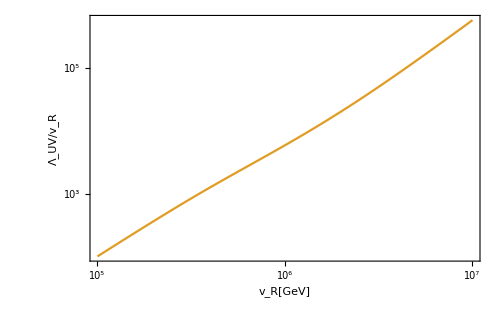

```mathematica
plot1TeV=ListLinePlot[{#1,Log10[#2]}&@@@list1TeV,InterpolationOrder->3,BaseStyle->{FontSize->24,FontFamily->"Times"},Frame->True,FrameLabel->{Style["v_R[GeV]",FontFamily->"Times",FontSize->24],Style["Λ_UV/v_R",FontFamily->"Times",FontSize->24]},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,FrameTicks->{{myTicks[-1,6,1],None},{myTicks[4,8,1],None}},PlotStyle->ColorData[97,2],PlotRange->{{5,7},Automatic}]
```

## Extra fermion at 2TeV scale

```mathematica
βyt[λ_,yt_,g3_,g2_,g1_,yN_]:=2yt(κ yt^2(3/4+1/2 dR)+κ g3^2(-3CF)+3 κ^2 λ^2+(-6)κ^2 yt^2 λ+κ^2 yt^4(3/4-9/4 dR)+κ^2 g3^2 yt^2(6CF+5/2 CF dR)+κ^2 g3^4(-3/2 CF^2-97/6 CA CF+10/3 Nf TR CF)+κ^3 λ^3(-18)+κ^3 yt^2 λ^2(285/8-45/4 dR)+κ^3 yt^4 λ(63/2+45/2 dR)+κ^3 yt^6(-345/32+107/32 dR+39/16 dR^2+9/4 z3+3/2 z3 dR)+κ^3 g3^2 yt^2 λ(6CF)+κ^3 g3^2 yt^4(-57/2 CF-81/8 CF dR)+κ^3 g3^4 yt^2(471/16 CF^2-119/8 CF^2 dR+25TR CF+717/16 CA CF+77/4 CA CF dR-33/4 Nf TR CF-4Nf TR CF dR-27z3 CF^2+18z3 CF^2 dR-27/2 z3 CA CF-9 z3 CA CF dR)+κ^3 g3^6(-129/2 CF^3+129/4 CA CF^2-11413/108 CA^2 CF+46Nf TR CF^2+556/27 Nf CA TR CF+140/27 Nf^2 TR^2 CF-48z3 Nf TR CF^2+48z3 Nf CA TR CF))+
yt κ(-9/4 g2^2-17/12 g1^2)+
yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45 Ng)+58/57 g1^4*2-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-Ng)g2^4+9 g2^2 g3^2);
βg3[λ_,yt_,g3_,g2_,g1_,yN_]:=2g3(κ g3^2(-11/6 CA+2/3 Nf TR)+κ^2 g3^2 yt^2(-2TR)+κ^2 g3^4(-17/3 CA^2+2Nf TR CF+10/3 Nf CA TR)+κ^3 g3^2 yt^4(9/2 TR+7/2 TR dR)+κ^3 g3^4 yt^2(-3TR CF-12CA TR)+κ^3 g3^6(-2857/108 CA^3-Nf TR CF^2+205/18 Nf CA TR CF+1415/54 Nf CA^2 TR-22/9 Nf^2 TR^2 CF-79/27 Nf^2 CA TR^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_,yN_]:=-g1^3 κ(-1/6-20/9 Ng+2/3*2)+g1^3 κ^2 5/3(199/30 g1^2+6/5*2 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_,yN_]:=-g2^3 κ(43/6-4/3 Ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);
βλ[λ_,yt_,g3_,g2_,g1_,t_,yN_]:=2(12κ λ^2+2κ yt^2 λ dR+κ yt^4(-dR)+κ (yN SmoothUnitStep[t-Log[2000/mZ]])^4(-2)+κ^2 λ^3(-156)+κ^2 yt^2 λ^2(-24dR)+κ^2 yt^4 λ(-1/2 dR)+κ^2 yt^6(5dR)+κ^2 g3^2 yt^2 λ(10CF dR)+κ^2 g3^2 yt^4(-4CF dR)+κ^3 λ^4(3588+2016z3)+κ^3 yt^2 λ^3(291dR)+κ^3 yt^4 λ^2(789/2 dR-36 dR^2+252z3 dR)+κ^3 yt^6 λ(-1881/8 dR+80 dR^2-66z3 dR)+κ^3 yt^8(13/2 dR-195/8 dR^2-12z3 dR)+κ^3 g3^2 yt^2 λ^2(-306CF dR+288z3 CF dR)+κ^3 g3^2 yt^4 λ(895/4 CF dR-324 z3 CF dR)+κ^3 g3^2 yt^6(-19/2 CF dR+60z3 CF dR)+κ^3 g3^2 yt^2 λ(-119/2 CF^2 dR+77CA CF dR-16Nf TR CF dR+72z3 CF^2 dR-36z3 CA CF dR)+κ^3 g3^4 yt^4(131/2 CF^2 dR+48TR CF dR-109/2 CA CF dR+10Nf TR CF dR-48z3 CF^2 dR+24z3 CA CF dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10Ng)g2^4-39/4 g2^2 g1^2-(687/200+2Ng)25/9 g1^4+60/19*2 g1^4)2λ+(497/8-8Ng)g2^6-(97/40+8/5 Ng)5/3 g2^4 g1^2-(717/200+8/5 Ng)25/9 g2^2 g1^4-(531/1000+24/25 Ng)125/27 g1^6-1728/505*2 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10 *2 λ yt^2(17/12 g1^2+9/4 g2^2));
```

```mathematica
list2TeV={};
```

## v_R=10^5.5 GeV

```mathematica
vR=10^5.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.6,0.8,0.01}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.77}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.72}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 7.29529×10^19+6.58056×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

FindMinimum::nrnum: The function value 6.83016×10^19+6.54963×10^19 ⅈ is not a real number at {ϕ} = {316228.}.

FindMinimum::nrnum: The function value -2.58741×10^14 ((0.-1213.7 ⅈ)+Null)+1.51661×10^10 ((1.47308×10^8+0. ⅈ)+((0.-1213.7 ⅈ)+Null)^2)-(((0.-1213.7 ⅈ)+Null) (4.57015×10^-32+2 («1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((0.-1213.7 ⅈ)+Null) (1.44521×10^15+2 (9.03111×10^14-Plus[«1»]^(3/2))-«19» («1»)^(«1»)-Abs[6.39132×10^9+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^21 (-0.00922349-1.89977×10^-24 (1.74589×10^20 Log[Times[«2»]]+1.63396×10^20 Log[Times[«2»]]-2.22717×10^21 Log[Times[«2»]]-2.73067×10^21 Log[Times[«2»]])) is not a real number at {ϕ} = {316228.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,316228.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.760239

0.718552

```mathematica
tab={};
For[i=3,i<10,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

{{1.×10^7,957.453,179.22},{3.16228×10^7,654.153,99.2146},{1.×10^8,485.16,62.6958},{3.16228×10^8,380.37,42.2323},{1.×10^9,310.919,29.9478},{3.16228×10^9,262.256,22.1883},{1.×10^10,226.528,17.0497}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,11}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list2TeV,{5.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{435.836}

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

8.20609

1.61043×10^8

509.261

## v_R=10^6 GeV

```mathematica
vR=10^6;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.5,0.76,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.6}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 3.88258×10^21+4.63727×10^21 ⅈ is not a real number at {ϕ} = {1.×10^6}.

FindMinimum::nrnum: The function value 3.48383×10^21+4.59374×10^21 ⅈ is not a real number at {ϕ} = {1.×10^6}.

FindMinimum::nrnum: The function value -8.01955×10^15 ((0.-5606.35 ⅈ)+Null)+1.37116×10^11 ((3.14312×10^9+0. ⅈ)+((0.-5606.35 ⅈ)+Null)^2)-(((0.-5606.35 ⅈ)+Null) (4.50782×10^-32+2 («24»-«1»)-«1»-Abs[«1»]^(3/2)))/(12 π)+(((0.-5606.35 ⅈ)+Null) (4.50782×10^16+2 (2.78492×10^16-Plus[«2»]^(3/2))-0.353553 «1»-Abs[6.33307×10^10+Times[«2»]+Times[«2»]]^(3/2)))/(12 π)+2.5×10^23 (-0.00733325-(3 (1.68829×10^22 Log[Times[«2»]]+1.60431×10^22 Log[Times[«2»]]-1.94403×10^23 Log[Times[«2»]]-1.79159×10^23 Log[Times[«2»]]))/(16000000000000000000000000 π^2)) is not a real number at {ϕ} = {1.×10^6}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,1000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.685631

0.628861

```mathematica
tab={};
For[i=3,i<10,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.7022 and x = -20.7022.

{{3.16228×10^7,1736.95,422.044},{1.×10^8,1053.87,183.441},{3.16228×10^8,745.131,105.173},{1.×10^9,569.638,67.5704},{3.16228×10^9,458.417,46.603},{1.×10^10,382.579,33.8962},{3.16228×10^10,327.922,25.7017}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,11}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list2TeV,{6.0,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{440.442}

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

9.60256

4.00559×10^9

4005.59

## v_R=10^6.5 GeV

```mathematica
vR=10^6.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.4,0.7,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.6}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.32754×10^23+3.25079×10^23 ⅈ is not a real number at {ϕ} = {3.16228×10^6}.

FindMinimum::nrnum: The function value 8.6054×10^22+3.18423×10^23 ⅈ is not a real number at {ϕ} = {3.16228×10^6}.

FindMinimum::nrnum: The function value 3.93109×10^22+3.11892×10^23 ⅈ is not a real number at {ϕ} = {3.16228×10^6}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,3.16228×10^6} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.62319

0.554489

```mathematica
tab={};
For[i=5,i<12,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -15.9591 and x = -15.9591.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -21.3623 and x = -21.3623.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -21.826 and x = -21.826.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

NDSolve::ndsz: At x == -24.0768, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == -24.4799, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == -24.5259, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.21748×10^-11}. NIntegrate obtained 87.034 and 0.0809151 for the integral and error estimates.

{{1.×10^9,1100.27,170.168},{3.16228×10^9,816.853,103.723},{1.×10^10,645.989,69.395},{3.16228×10^10,532.91,49.479},{1.×10^11,453.022,36.99},{3.16228×10^11,393.763,28.682},{1.×10^12,719.637,394.401}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,11}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list2TeV,{6.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{445.047}

11.0308

1.07353×10^11

33948.1

## v_R=10^7 GeV

```mathematica
vR=10^7;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR],
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc,
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
λ10vR=-4 V0T[10vR]/(10vR)^4;
action=(8 π^2)/(3λ10vR)
}
,{yN,0.4,0.6,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.5}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.5}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
vR=10^4;
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.31803×10^25+2.47028×10^25 ⅈ is not a real number at {ϕ} = {1.×10^7}.

FindMinimum::nrnum: The function value 9.71239×10^24+2.41193×10^25 ⅈ is not a real number at {ϕ} = {1.×10^7}.

FindMinimum::nrnum: The function value 6.25657×10^24+2.35439×10^25 ⅈ is not a real number at {ϕ} = {1.×10^7}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,10000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.568584

0.48645

```mathematica
tab={};
For[i=6,i<14,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab(*Here the escape point unit should be TeV!*)
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -15.9254 and x = -15.9254.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.5235 and x = -20.5235.

{{1.×10^7,1157.69,158.878},{3.16228×10^7,895.782,102.413},{1.×10^8,728.662,71.2991},{3.16228×10^8,613.383,52.4201},{1.×10^9,529.307,40.146},{3.16228×10^9,465.369,31.7325},{1.×10^10,415.145,25.7183},{3.16228×10^10,374.667,21.271}}

```mathematica
vR=10^7;(*Back to GeV*)
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,10}]
escapefinal=10^(escape+3)+vR
escapefinal/vR
AppendTo[list2TeV,{7,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{449.652}

9.6442

4.40761×10^12

440761.

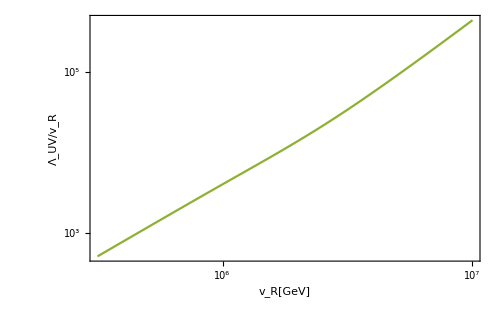

```mathematica
plot2TeV=ListLinePlot[{#1,Log10[#2]}&@@@list2TeV,InterpolationOrder->3,BaseStyle->{FontSize->24,FontFamily->"Times"},Frame->True,FrameLabel->{Style["v_R[GeV]",FontFamily->"Times",FontSize->24],Style["Λ_UV/v_R",FontFamily->"Times",FontSize->24]},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->24]},PlotRangePadding->None,ImageSize->500,FrameTicks->{{myTicks[-1,6,1],None},{myTicks[4,8,1],None}},PlotStyle->ColorData[97,3]]
```

## Combine

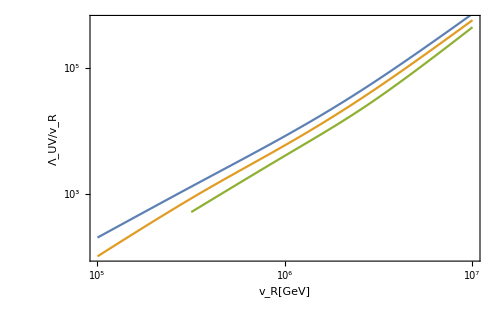

```mathematica
Show[{plot1TeV,plot2TeV,plot500GeV},Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},{Style["500 GeV",FontFamily->"Times",FontSize->18],Style["1 TeV",FontFamily->"Times",FontSize->18],Style["2 TeV",FontSize->18,FontFamily->"Times"]}]}],RoundingRadius->5],Scaled[{0.18,0.72}]]}]
```